```mathematica
incr[digs_,base_]:=Module[{carry=1,ndigs=digs,k=1,nd},While[k≤Length[digs],{carry,nd}=QuotientRemainder[Part[ndigs,k]+carry,Part[base,k]];
Part[ndigs,k]=nd;
If[carry==0,Break[]];k++;];
ndigs];
t[i_,j_]:=2.Min[i,j]-1.KroneckerDelta[i,j];
UpB[L_,M_,α_,n_]:=(L-1.-Sum[t[n,j]α[[j]],{j,1.,M}])/2.;

GenString[M_]:=Block[{part,part1,pair,d,j,k,m,p,
check},
m=M;
part=Reap[While[m!=0,
d=IntegerPart[RandomReal[{1.,M+1-10^(-12)}]];
j=IntegerPart[RandomReal[{1.,M+1-10^(-12)}]];
p=RandomReal[{0,1}];
If[p<=(d PartitionsP[m-j d])/(m PartitionsP[m]),
Sow[Table[d,{k,1,j}]];
m=m-j d;];];];
(* Convert the partition to standard string format *)
part1=Flatten[part];
Table[Count[part1,i],{i,1,M}]];
(* Markov chain: Given a string configuration it generate the *)
(* next one with the right probability *)

ChooString[M_,L_,strOl_]:=Block[{string,mat,DDol,DDne,i,j,
strNe,p,vec,vec1},
string=strOl;
mat=Table[t[i,j],{i,1,M},{j,1,M}];DDol=Product[
Binomial[L-Total[Table[mat[[i,j]]string[[j]],{j,1,M}]],
string[[i]]],{i,1,M}];

strNe=GenString[M];
DDne=Product[Binomial[L-Total[Table[mat[[i,j]]strNe[[j]],
{j,1,M}]],strNe[[i]]],{i,1,M}];
p=RandomReal[{0,1}];
If[p<=Min[1,DDne/DDol],string=strNe;];
string];

BTsel[M_,L_,α_]:=Block[{J,n,k},
J=Table[RandomSample[Table[k,{k,-UpB[L,M,α,n],
UpB[L,M,α,n]}],α[[n]]],{n,1,M}];J];

(* Scattering phases for the Bethe-Takahashi equations *)
Theta[x_,m_,n_]:=If[n!=m,2ArcTan[x/Abs[n-m]]+
4Sum[ArcTan[x/(Abs[n-m]+k)],{k,2,n+m-Abs[n-m]-2,2}]
+2ArcTan[x/(n+m)],4Sum[ArcTan[x/k],{k,2,2n-2,2}]+
2ArcTan[x/(2n)]];

(*Solution of the Bethe-Takahashi equations*)
SolveBethe[M_,L_,string_,BN_]:=Block[{sol,x,n,g,b,m,o,h,check,sol1,bit,EE,EE1,EE2,EE3},
check=1;
bit=0;
sol=Table[x[n][g],{n,1,M},{g,1,string[[n]]}]/.FindRoot[
Flatten[Table[ArcTan[x[n][g]/n]-π BN[[n,g]]/L-1/(2L)
∑_(m=1)^M ∑_(b=1)^string[[m]] If[m!=n||b!=g,Theta[x[n][g]-x[m][b],m,n],
0]==0,{n,1,M},{g,1,string[[n]]}]],Flatten[Table[
{x[o][h],RandomReal[]},{o,1,M},{h,1,string[[o]]}],1],
WorkingPrecision->15,MaxIterations->200,AccuracyGoal->15]//
Quiet;

check=Flatten[Table[ArcTan[sol[[n]][[g]]/n]-π BN[[n,g]]/L-
1/(2L)∑_(m=1)^M ∑_(b=1)^string[[m]] If[m!=n||b!=g,Theta[sol[[n]][[g]]-
sol[[m]][[b]],m,n],0],{n,1,M},{g,1,string[[n]]}]];
If[Total[Abs[check]]>10^-11,Print["Findroot failed with string"];
Print[BN];
bit=1;];
EE=If[M!=0,((*-L/4*)+Total[Flatten[Table[2.n/((sol[[n,g]])^2.+n^2.),
{n,1,M},{g,1,string[[n]]}]]]),-L/4];
(*Print[string];
Print[BN];
Print[sol];*)
(*Flatten[*){bit,EE ,BN,Chop[sol]}(*]*)
];

(*For the quench action*)
(*Select the parity invariant eigenstates*)
PIState[string_,BN_]:=Module[{BN1,BN2,i,check,tot},
BN1=Table[Sort[-BN[[i]]],{i,1,Length[BN]}];
BN2=Flatten[BN1];
check=Select[BN2,Abs[#]<10^-13&];

tot=Select[Flatten[BN],Abs[#]>0&];
(*Print[BN];*)

If[BN==BN1(*&&EvenQ[Length[tot]]*)&&check=={},0,1]];

(*Select strings with non-zero centers*)
NonZeroRap[rap_]:=Module[{rap1,check},
rap1=Flatten[rap];
check=Select[rap1,Abs[#]<10^-12&];
If[check=={},0,1]
];

(*Derivative of θ(x)*)
Dtheta[x_,n_]:=(2 n)/(n^2+x^2);

(* Derivative of the scattering phases for the Bethe-Takahashi equations *)
DTheta[x_,m_,n_]:=If[n!=m,(2 Abs[m-n])/(x^2+Abs[m-n]^2)+
4Sum[(k+ Abs[m-n])/(x^2+(k+Abs[m-n])^2),{k,2,n+m-Abs[n-m]-2,2}]
+(2 (m+n))/((m+n)^2+x^2),4Sum[k/(k^2+x^2),{k,2,2n-2,2}]+
(4 n)/(4 n^2+x^2)];

(*Construct the prefactor in the Neel overlap expression*)
PP[x_,n_]:=Module[{k},If[OddQ[n],1/4^n(x/(√(n^2+x^2))Product[((2k+1)^2+x^2)/((2k)^2+x^2),{k,0,Floor[n/2]}]),1/4^n((√(n^2+x^2))/x Product[((2k)^2+x^2)/((2k+1)^2+x^2),{k,0,Floor[n/2]-1}])]
];


(*Construct the matrix elements of G- as defined in J-S paper*)
CGm[i1_,j1_,i2_,j2_,string_,rap_]:=Module[{k,l},If[i1≠i2||j1≠j2,2(DTheta[rap[[i1,j1]]-rap[[i2,j2]],i1,i2]-DTheta[rap[[i1,j1]]+rap[[i2,j2]],i1,i2]),
2(L-1)Dtheta[rap[[i1,j1]],i1]-4Sum[Dtheta[rap[[i1,j1]],k],{k,1,i1-1}]-2Sum[If[i1≠k||j1≠l,DTheta[rap[[i1,j1]]-rap[[k,l]],i1,k]+DTheta[rap[[i1,j1]]+rap[[k,l]],i1,k],0],{k,1,Length[string]},{l,1,string[[k]]}]
]
];
(*Construct the matrix elements of G+ as defined in J-S paper*)
CGp[i1_,j1_,i2_,j2_,string_,rap_]:=Module[{k,l},If[i1≠i2||j1≠j2,2(DTheta[rap[[i1,j1]]-rap[[i2,j2]],i1,i2]+DTheta[rap[[i1,j1]]+rap[[i2,j2]],i1,i2]),
2(L)Dtheta[rap[[i1,j1]],i1]-2Sum[If[i1≠k||j1≠l,DTheta[rap[[i1,j1]]-rap[[k,l]],i1,k]+DTheta[rap[[i1,j1]]+rap[[k,l]],i1,k],0],{k,1,Length[string]},{l,1,string[[k]]}]
]
];

(*Calculate the overlap with the Neel state*)
Overlap[string_,rap_,NI_]:=Module[{indx,ll,i,j,GGm,GGp},
indx=Flatten[Table[Table[{i,j},{j,1,string[[i]]}],{i,1,Length[string]}],1];
ll=Total[string];
GGm=Table[CGm[indx[[i,1]],indx[[i,2]],indx[[j,1]],indx[[j,2]],string,rap],{i,1,ll},{j,1,ll}];
GGp=Table[CGp[indx[[i,1]],indx[[i,2]],indx[[j,1]],indx[[j,2]],string,rap],{i,1,ll},{j,1,ll}];
(2^(1/2)(NI!)/((2NI)!)^(1/2)Product[PP[rap[[i,j]],i],{i,1,Length[string]},{j,1,string[[i]]}](Det[GGp]/Det[GGm])^(1/2))^2];

(*Overlap with zero-momentum string*)
KK1[x_]:=2/(x^2+1);
KK12[x_]:=1/(x^2+1/4);
Kp[x_,y_]:=KK1[x-y]+KK1[x+y];
Km[x_,y_]:=KK1[x-y]-KK1[x+y];
Gp[j_,k_,rap_]:=KroneckerDelta[j,k](L KK12[rap[[j]]]-Sum[Kp[rap[[j]],rap[[p]]],{p,1,Length[rap]}])+Kp[rap[[j]],rap[[k]]];
Gm[j_,k_,rap_]:=KroneckerDelta[j,k](L KK12[rap[[j]]]-Sum[Kp[rap[[j]],rap[[p]]],{p,1,Length[rap]}])+Km[rap[[j]],rap[[k]]];

index[string_,k_]:=Module[{z,cont},
cont=1;
z=k;
While[z>0,
z=z-string[[cont]];
cont++;
];
cont-1
];

OverlapAll[string_,rap1_,NI_]:=Module[{rap,rapstring,rpstr1,k,ll,i,j,GGm,GGp},
rapstring={};
rap=Flatten[rap1];
For[k=1,k≤Length[rap],k++,
AppendTo[rapstring,Table[rap[[k]]/2+RandomReal[{10^-5,10^-6}]+(1+RandomReal[{10^-5,10^-6}])I/2.(index[string,k]+1-2j),{j,1,index[string,k]}]];
];
rpstr1=Flatten[rapstring];
ll=Length[rpstr1];
(*Print[rpstr1];*)
GGp=Table[Gp[i,j,rpstr1],{i,1,ll},{j,1,ll}];
GGm=Table[Gm[i,j,rpstr1],{i,1,ll},{j,1,ll}];

(2^(1/2)(NI!)/((2NI)!)^(1/2)Product[((rpstr1[[j]]^2+1/4)^(1/2))/(4rpstr1[[j]]),{j,1,ll}](Det[GGp]/Det[GGm])^(1/2))^2
];




L=12;
data=Reap[For[i=1,i≤L/2,i++,
M=i;
NI=L/2-i;
base=Table[IntegerPart[M/j]+1,{j,1,M}];

initial=Table[0,{k,1,M}];
For[r=1,r≤Product[base[[b]],{b,1,M}],r++,
If[Sum[s initial[[s]],{s,1,M}]==M,
For[z=1,z≤M,z++,
tab[z]=Subsets[Table[kk,{kk,-UpB[L,M,initial,z],UpB[L,M,initial,z]}],{initial[[z]]}];

];
res=Table[tab[i],{i,1,M}];
res1=Tuples[res];
For[pp=1,pp≤Length[res1],pp++,
(*Print[res1[[pp]]];*)
If[PIState[initial,res1[[pp]]]==0,
sol=SolveBethe[M,L,initial,res1[[pp]]];
If[(*NonZeroRap[sol[[4]]]==0*)1>0,
If[sol[[1]]==0,
string=Table[Length[sol[[3,k]]]/2,{k,1,Length[sol[[3]]]}];
rap1=Table[Sort[sol[[4,k]]],{k,1,Length[sol[[4]]]}];
rap=Table[Table[-rap1[[k,j]],{j,1,string[[k]]}],{k,1,Length[sol[[4]]]}];

overlap=Overlap[string,rap,NI];
overlapall=OverlapAll[string,rap,NI];

diff=overlap-overlapall;
Print[{res1[[pp]]}];

Sow[{overlap}]];
];];];
Clear[tab];
]
initial1=incr[initial,base];
initial=initial1;
]
]][[2]];
data1=Flatten[data,1];
```

{{-5.},{-4.},{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.},{4.},{5.}}

{{-4.5,-3.5},{-4.5,-2.5},{-4.5,-1.5},{-4.5,-0.5},{-4.5,0.5},{-4.5,1.5},{-4.5,2.5},{-4.5,3.5},{-4.5,4.5},{-3.5,-2.5},{-3.5,-1.5},{-3.5,-0.5},{-3.5,0.5},{-3.5,1.5},{-3.5,2.5},{-3.5,3.5},{-3.5,4.5},{-2.5,-1.5},{-2.5,-0.5},{-2.5,0.5},{-2.5,1.5},{-2.5,2.5},{-2.5,3.5},{-2.5,4.5},{-1.5,-0.5},{-1.5,0.5},{-1.5,1.5},{-1.5,2.5},{-1.5,3.5},{-1.5,4.5},{-0.5,0.5},{-0.5,1.5},{-0.5,2.5},{-0.5,3.5},{-0.5,4.5},{0.5,1.5},{0.5,2.5},{0.5,3.5},{0.5,4.5},{1.5,2.5},{1.5,3.5},{1.5,4.5},{2.5,3.5},{2.5,4.5},{3.5,4.5}}

{{}}

{{{-4.5,4.5},{}}}

{{{-3.5,3.5},{}}}

{{{-2.5,2.5},{}}}

{{{-1.5,1.5},{}}}

{{{-0.5,0.5},{}}}

{{}}

{{-4.},{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.},{4.}}

{{-4.,-3.,-2.},{-4.,-3.,-1.},{-4.,-3.,0.},{-4.,-3.,1.},{-4.,-3.,2.},{-4.,-3.,3.},{-4.,-3.,4.},{-4.,-2.,-1.},{-4.,-2.,0.},{-4.,-2.,1.},{-4.,-2.,2.},{-4.,-2.,3.},{-4.,-2.,4.},{-4.,-1.,0.},{-4.,-1.,1.},{-4.,-1.,2.},{-4.,-1.,3.},{-4.,-1.,4.},{-4.,0.,1.},{-4.,0.,2.},{-4.,0.,3.},{-4.,0.,4.},{-4.,1.,2.},{-4.,1.,3.},{-4.,1.,4.},{-4.,2.,3.},{-4.,2.,4.},{-4.,3.,4.},{-3.,-2.,-1.},{-3.,-2.,0.},{-3.,-2.,1.},{-3.,-2.,2.},{-3.,-2.,3.},{-3.,-2.,4.},{-3.,-1.,0.},{-3.,-1.,1.},{-3.,-1.,2.},{-3.,-1.,3.},{-3.,-1.,4.},{-3.,0.,1.},{-3.,0.,2.},{-3.,0.,3.},{-3.,0.,4.},{-3.,1.,2.},{-3.,1.,3.},{-3.,1.,4.},{-3.,2.,3.},{-3.,2.,4.},{-3.,3.,4.},{-2.,-1.,0.},{-2.,-1.,1.},{-2.,-1.,2.},{-2.,-1.,3.},{-2.,-1.,4.},{-2.,0.,1.},{-2.,0.,2.},{-2.,0.,3.},{-2.,0.,4.},{-2.,1.,2.},{-2.,1.,3.},{-2.,1.,4.},{-2.,2.,3.},{-2.,2.,4.},{-2.,3.,4.},{-1.,0.,1.},{-1.,0.,2.},{-1.,0.,3.},{-1.,0.,4.},{-1.,1.,2.},{-1.,1.,3.},{-1.,1.,4.},{-1.,2.,3.},{-1.,2.,4.},{-1.,3.,4.},{0.,1.,2.},{0.,1.,3.},{0.,1.,4.},{0.,2.,3.},{0.,2.,4.},{0.,3.,4.},{1.,2.,3.},{1.,2.,4.},{1.,3.,4.},{2.,3.,4.}}

{{}}

{{}}

{{-4.},{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.},{4.}}

{{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.}}

{{}}

{{}}

{{}}

{{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.}}

{{-3.5,-2.5,-1.5,-0.5},{-3.5,-2.5,-1.5,0.5},{-3.5,-2.5,-1.5,1.5},{-3.5,-2.5,-1.5,2.5},{-3.5,-2.5,-1.5,3.5},{-3.5,-2.5,-0.5,0.5},{-3.5,-2.5,-0.5,1.5},{-3.5,-2.5,-0.5,2.5},{-3.5,-2.5,-0.5,3.5},{-3.5,-2.5,0.5,1.5},{-3.5,-2.5,0.5,2.5},{-3.5,-2.5,0.5,3.5},{-3.5,-2.5,1.5,2.5},{-3.5,-2.5,1.5,3.5},{-3.5,-2.5,2.5,3.5},{-3.5,-1.5,-0.5,0.5},{-3.5,-1.5,-0.5,1.5},{-3.5,-1.5,-0.5,2.5},{-3.5,-1.5,-0.5,3.5},{-3.5,-1.5,0.5,1.5},{-3.5,-1.5,0.5,2.5},{-3.5,-1.5,0.5,3.5},{-3.5,-1.5,1.5,2.5},{-3.5,-1.5,1.5,3.5},{-3.5,-1.5,2.5,3.5},{-3.5,-0.5,0.5,1.5},{-3.5,-0.5,0.5,2.5},{-3.5,-0.5,0.5,3.5},{-3.5,-0.5,1.5,2.5},{-3.5,-0.5,1.5,3.5},{-3.5,-0.5,2.5,3.5},{-3.5,0.5,1.5,2.5},{-3.5,0.5,1.5,3.5},{-3.5,0.5,2.5,3.5},{-3.5,1.5,2.5,3.5},{-2.5,-1.5,-0.5,0.5},{-2.5,-1.5,-0.5,1.5},{-2.5,-1.5,-0.5,2.5},{-2.5,-1.5,-0.5,3.5},{-2.5,-1.5,0.5,1.5},{-2.5,-1.5,0.5,2.5},{-2.5,-1.5,0.5,3.5},{-2.5,-1.5,1.5,2.5},{-2.5,-1.5,1.5,3.5},{-2.5,-1.5,2.5,3.5},{-2.5,-0.5,0.5,1.5},{-2.5,-0.5,0.5,2.5},{-2.5,-0.5,0.5,3.5},{-2.5,-0.5,1.5,2.5},{-2.5,-0.5,1.5,3.5},{-2.5,-0.5,2.5,3.5},{-2.5,0.5,1.5,2.5},{-2.5,0.5,1.5,3.5},{-2.5,0.5,2.5,3.5},{-2.5,1.5,2.5,3.5},{-1.5,-0.5,0.5,1.5},{-1.5,-0.5,0.5,2.5},{-1.5,-0.5,0.5,3.5},{-1.5,-0.5,1.5,2.5},{-1.5,-0.5,1.5,3.5},{-1.5,-0.5,2.5,3.5},{-1.5,0.5,1.5,2.5},{-1.5,0.5,1.5,3.5},{-1.5,0.5,2.5,3.5},{-1.5,1.5,2.5,3.5},{-0.5,0.5,1.5,2.5},{-0.5,0.5,1.5,3.5},{-0.5,0.5,2.5,3.5},{-0.5,1.5,2.5,3.5},{0.5,1.5,2.5,3.5}}

{{}}

{{}}

{{}}

{{{-3.5,-2.5,2.5,3.5},{},{},{}}}

{{{-3.5,-1.5,1.5,3.5},{},{},{}}}

{{{-3.5,-0.5,0.5,3.5},{},{},{}}}

{{{-2.5,-1.5,1.5,2.5},{},{},{}}}

{{{-2.5,-0.5,0.5,2.5},{},{},{}}}

{{{-1.5,-0.5,0.5,1.5},{},{},{}}}

{{-3.5,-2.5},{-3.5,-1.5},{-3.5,-0.5},{-3.5,0.5},{-3.5,1.5},{-3.5,2.5},{-3.5,3.5},{-2.5,-1.5},{-2.5,-0.5},{-2.5,0.5},{-2.5,1.5},{-2.5,2.5},{-2.5,3.5},{-1.5,-0.5},{-1.5,0.5},{-1.5,1.5},{-1.5,2.5},{-1.5,3.5},{-0.5,0.5},{-0.5,1.5},{-0.5,2.5},{-0.5,3.5},{0.5,1.5},{0.5,2.5},{0.5,3.5},{1.5,2.5},{1.5,3.5},{2.5,3.5}}

{{-2.},{-1.},{0.},{1.},{2.}}

{{}}

{{}}

{{}}

{{-2.5,-1.5},{-2.5,-0.5},{-2.5,0.5},{-2.5,1.5},{-2.5,2.5},{-1.5,-0.5},{-1.5,0.5},{-1.5,1.5},{-1.5,2.5},{-0.5,0.5},{-0.5,1.5},{-0.5,2.5},{0.5,1.5},{0.5,2.5},{1.5,2.5}}

{{}}

{{}}

{{{},{-2.5,2.5},{},{}}}

{{{},{-1.5,1.5},{},{}}}

{{{},{-0.5,0.5},{},{}}}

{{-4.},{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.},{4.}}

{{}}

{{-2.},{-1.},{0.},{1.},{2.}}

{{}}

{{}}

{{}}

«1 more identical outputs»

{{-2.},{-1.},{0.},{1.},{2.}}

{{-3.,-2.,-1.,0.,1.},{-3.,-2.,-1.,0.,2.},{-3.,-2.,-1.,0.,3.},{-3.,-2.,-1.,1.,2.},{-3.,-2.,-1.,1.,3.},{-3.,-2.,-1.,2.,3.},{-3.,-2.,0.,1.,2.},{-3.,-2.,0.,1.,3.},{-3.,-2.,0.,2.,3.},{-3.,-2.,1.,2.,3.},{-3.,-1.,0.,1.,2.},{-3.,-1.,0.,1.,3.},{-3.,-1.,0.,2.,3.},{-3.,-1.,1.,2.,3.},{-3.,0.,1.,2.,3.},{-2.,-1.,0.,1.,2.},{-2.,-1.,0.,1.,3.},{-2.,-1.,0.,2.,3.},{-2.,-1.,1.,2.,3.},{-2.,0.,1.,2.,3.},{-1.,0.,1.,2.,3.}}

{{}}

{{}}

{{}}

«1 more identical outputs»

{{-3.,-2.,-1.},{-3.,-2.,0.},{-3.,-2.,1.},{-3.,-2.,2.},{-3.,-2.,3.},{-3.,-1.,0.},{-3.,-1.,1.},{-3.,-1.,2.},{-3.,-1.,3.},{-3.,0.,1.},{-3.,0.,2.},{-3.,0.,3.},{-3.,1.,2.},{-3.,1.,3.},{-3.,2.,3.},{-2.,-1.,0.},{-2.,-1.,1.},{-2.,-1.,2.},{-2.,-1.,3.},{-2.,0.,1.},{-2.,0.,2.},{-2.,0.,3.},{-2.,1.,2.},{-2.,1.,3.},{-2.,2.,3.},{-1.,0.,1.},{-1.,0.,2.},{-1.,0.,3.},{-1.,1.,2.},{-1.,1.,3.},{-1.,2.,3.},{0.,1.,2.},{0.,1.,3.},{0.,2.,3.},{1.,2.,3.}}

{{-1.},{0.},{1.}}

{{}}

{{}}

{{}}

{{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.}}

{{-1.5,-0.5},{-1.5,0.5},{-1.5,1.5},{-0.5,0.5},{-0.5,1.5},{0.5,1.5}}

{{}}

{{}}

{{}}

{{-3.5,-2.5},{-3.5,-1.5},{-3.5,-0.5},{-3.5,0.5},{-3.5,1.5},{-3.5,2.5},{-3.5,3.5},{-2.5,-1.5},{-2.5,-0.5},{-2.5,0.5},{-2.5,1.5},{-2.5,2.5},{-2.5,3.5},{-1.5,-0.5},{-1.5,0.5},{-1.5,1.5},{-1.5,2.5},{-1.5,3.5},{-0.5,0.5},{-0.5,1.5},{-0.5,2.5},{-0.5,3.5},{0.5,1.5},{0.5,2.5},{0.5,3.5},{1.5,2.5},{1.5,3.5},{2.5,3.5}}

{{}}

{{-1.},{0.},{1.}}

{{}}

{{}}

{{}}

{{-2.},{-1.},{0.},{1.},{2.}}

{{-1.},{0.},{1.}}

{{}}

{{}}

{{-4.},{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.},{4.}}

{{}}

{{}}

{{-1.},{0.},{1.}}

{{}}

{{}}

{{}}

«2 more identical outputs»

{{-1.},{0.},{1.}}

{{-2.5,-1.5,-0.5,0.5,1.5,2.5}}

{{}}

{{}}

{{}}

«2 more identical outputs»

{{{-2.5,-1.5,-0.5,0.5,1.5,2.5},{},{},{},{},{}}}

{{-2.5,-1.5,-0.5,0.5},{-2.5,-1.5,-0.5,1.5},{-2.5,-1.5,-0.5,2.5},{-2.5,-1.5,0.5,1.5},{-2.5,-1.5,0.5,2.5},{-2.5,-1.5,1.5,2.5},{-2.5,-0.5,0.5,1.5},{-2.5,-0.5,0.5,2.5},{-2.5,-0.5,1.5,2.5},{-2.5,0.5,1.5,2.5},{-1.5,-0.5,0.5,1.5},{-1.5,-0.5,0.5,2.5},{-1.5,-0.5,1.5,2.5},{-1.5,0.5,1.5,2.5},{-0.5,0.5,1.5,2.5}}

{{0.}}

{{}}

{{}}

{{}}

«1 more identical outputs»

{{-2.5,-1.5},{-2.5,-0.5},{-2.5,0.5},{-2.5,1.5},{-2.5,2.5},{-1.5,-0.5},{-1.5,0.5},{-1.5,1.5},{-1.5,2.5},{-0.5,0.5},{-0.5,1.5},{-0.5,2.5},{0.5,1.5},{0.5,2.5},{1.5,2.5}}

{{-0.5,0.5}}

{{}}

{{}}

{{}}

«1 more identical outputs»

{{{-2.5,2.5},{-0.5,0.5},{},{},{},{}}}

{{{-1.5,1.5},{-0.5,0.5},{},{},{},{}}}

{{{-0.5,0.5},{-0.5,0.5},{},{},{},{}}}

{{}}

{{-1.,0.,1.}}

{{}}

{{}}

{{}}

«1 more identical outputs»

{{-3.,-2.,-1.},{-3.,-2.,0.},{-3.,-2.,1.},{-3.,-2.,2.},{-3.,-2.,3.},{-3.,-1.,0.},{-3.,-1.,1.},{-3.,-1.,2.},{-3.,-1.,3.},{-3.,0.,1.},{-3.,0.,2.},{-3.,0.,3.},{-3.,1.,2.},{-3.,1.,3.},{-3.,2.,3.},{-2.,-1.,0.},{-2.,-1.,1.},{-2.,-1.,2.},{-2.,-1.,3.},{-2.,0.,1.},{-2.,0.,2.},{-2.,0.,3.},{-2.,1.,2.},{-2.,1.,3.},{-2.,2.,3.},{-1.,0.,1.},{-1.,0.,2.},{-1.,0.,3.},{-1.,1.,2.},{-1.,1.,3.},{-1.,2.,3.},{0.,1.,2.},{0.,1.,3.},{0.,2.,3.},{1.,2.,3.}}

{{}}

{{0.}}

{{}}

{{}}

{{}}

{{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.}}

{{-1.},{0.},{1.}}

{{0.}}

{{}}

{{}}

{{}}

«2 more identical outputs»

{{-0.5,0.5}}

{{}}

{{}}

{{}}

{{{},{},{-0.5,0.5},{},{},{}}}

{{-3.5,-2.5},{-3.5,-1.5},{-3.5,-0.5},{-3.5,0.5},{-3.5,1.5},{-3.5,2.5},{-3.5,3.5},{-2.5,-1.5},{-2.5,-0.5},{-2.5,0.5},{-2.5,1.5},{-2.5,2.5},{-2.5,3.5},{-1.5,-0.5},{-1.5,0.5},{-1.5,1.5},{-1.5,2.5},{-1.5,3.5},{-0.5,0.5},{-0.5,1.5},{-0.5,2.5},{-0.5,3.5},{0.5,1.5},{0.5,2.5},{0.5,3.5},{1.5,2.5},{1.5,3.5},{2.5,3.5}}

{{}}

{{}}

{{0.}}

{{}}

{{}}

{{}}

{{-2.},{-1.},{0.},{1.},{2.}}

{{}}

{{0.}}

{{}}

{{}}

{{-4.},{-3.},{-2.},{-1.},{0.},{1.},{2.},{3.},{4.}}

{{}}

{{}}

{{}}

{{0.}}

{{}}

{{}}

{{}}

«3 more identical outputs»

{{0.}}

```mathematica
over=Table[data1[[i,1]],{i,1,Length[data1]}];
{L,Total[over]}
```

{12,0.8790723405402}

```mathematica
data1[[2]]
```

{{0,0.521982,{{-6.5,6.5},{}},{{-2.5812975542009,2.5812975542009},{}}},0.00004435213231834}

```mathematica
Total[over]
```

0.9259703919453

```mathematica
test={{10,0.92597039194525020799343870249503184865`13.757864614143442},{12,0.87907234054024518573858701149879289464`13.649658292608681},{14,0.86405008609041731874489764427269560155`13.550304386690819},{16,0.82270298913304039509402966617665527231`13.47530720006427},{18,0.80211589828992383399496090784146204615`13.403532008280925},{20,0.76726841689649905290830538130054364212`13.34403594085183},{22,0.74701330410312566689719206270202426107`13.287816714331735},{24,0.71726717849049688026573494010965903176`13.23822475571535}};
test1=Table[{1/test[[i,1]],test[[i,2]]},{i,1,Length[test]}];
Export["/u/he/valba/Dropbox/ETH/GGE/notes/test.dat",test]
```

/u/he/valba/Dropbox/ETH/GGE/notes/test.dat

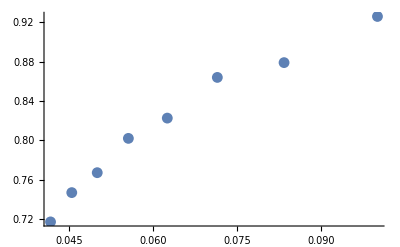

```mathematica
ListPlot[test1,PlotRange->{{},{}}]
```

```mathematica
2^0.5/2
```

0.707107

```mathematica
1/144.
```

0.00694444

```mathematica
Length[data1]
```

1713

```mathematica
2 1./Binomial[L,L/2]
```

0.0001554

```mathematica
over
```

{0.007864405079387,0.01183394577112,0.027777777777779,0.23030164914949,0.02354341388156,0.1947958643116,0.4171986420855,0.006842342041641,0.005812351847134}

```mathematica
L=18;
string={0,2,0,0,0,0,0,0,0};
Overlap[string,{{},{2.24141462891188237048388078380337158526`15.,0.93448729609517445048677383016840373238`15.},{},{},{},{},{},{},{}},1]
```

0.00003515046504622

```mathematica
0.11688311+0.5548097+0.00546870+0.15341215+0.00134247+0.04613475
```

0.878051

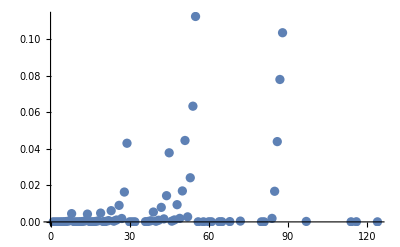

```mathematica
ListPlot[over, PlotRange->All]
```

```mathematica
over
```

{0.00211600620264,0.002752622983588,0.004542580506185,0.011288497946467,0.096183409244237,0.004059780227615,0.01009111350449,0.08599243602431,0.01525639552315,0.1292770236866,0.3101330338378,0.00193900139605,0.002325724713201,0.0012072454062882,0.153412152966,0.00133733403575,0.004730512604802,0.04104248891334,0.001384980817718}

```mathematica
string={1,1,0,0,0,0};
rappp={1.39026569574347852426731169625922706559`15.,0.69611293735619413561097939846616179936`15.};
OverlapAll[string,rappp,3]
```

{0.695133+0. ⅈ,0.348056+0.500002 ⅈ,0.348056-0.500004 ⅈ}

```mathematica
index[string,2]
```

2

```mathematica
string={2,0,0,0};
rap={{2.18244196845044095827771995392892086786`15.,0.9399875643884153852497220590594652723`15.},{},{},{}};
OverlapAll[string,rap,2]
```

{1.09122+0. ⅈ,0.469994+0. ⅈ}

0.00405978+0. ⅈ

```mathematica
Chop[data1]
```

{{ComplexInfinity},{0},{ComplexInfinity},{ComplexInfinity},{0.00405978},{0.0100911},{0.0859924},{0.0152564},{0.129277},{0.310133},{ComplexInfinity},{0},{ComplexInfinity},{ComplexInfinity},{ComplexInfinity},{ComplexInfinity},{ComplexInfinity},{ComplexInfinity},{0},{0},{0},{0.00133733},{0.00473051},{0.0410425},{ComplexInfinity},{0},{ComplexInfinity},{0}}

```mathematica
EvenQ[4]+EvenQ[3]
```

False+True

```mathematica
Select[{0.,3.,4.},#>0&]
```

{3.,4.}

```mathematica
Chop[data1]
```

{{2.30346},{0.00211515},{0.00274807},{0.00451919},{0.0106468},{0.0925971},{7.30718×10^-8+9.3738×10^-9 ⅈ},{5.04792},{61.313},{5.18533},{276.986},{0.000131932+0.0000580217 ⅈ},{0.00407811-0.000307448 ⅈ},{0.00399036},{0.0097912},{0.0703578},{0.014805},{0.103164},{0.255266},{2.06709×10^-8+5.13396×10^-9 ⅈ},{3.05323×10^-8+7.11982×10^-9 ⅈ},{1.91026×10^-7-6.0057×10^-8 ⅈ},{1.83583×10^-6-3.42022×10^-7 ⅈ},{0.00193438+2.0637×10^-6 ⅈ},{0.00230426-2.42854×10^-6 ⅈ},{0.00104462-0.0000725501 ⅈ},{47.1969+34.8371 ⅈ},{5.54845×10^-9-1.63547×10^-9 ⅈ},{5.12659},{26.22},{71.7099},{0.0000728089+0.0000570458 ⅈ},{0.00363422-0.00341375 ⅈ},{0.000407385+0.00024812 ⅈ},{10.7603-0.0337638 ⅈ},{7.26578+0.043383 ⅈ},{0.00135017+0.00180552 ⅈ},{0.00100881-0.000490172 ⅈ},{0.0140439-0.0130103 ⅈ},{0.421283-0.0850983 ⅈ},{-5.46899×10^-9-7.58442×10^-10 ⅈ},{3.83647×10^-6+2.0838×10^-6 ⅈ},{0.000306296-0.0000724024 ⅈ},{0.141533},{1.95937×10^-8+1.06601×10^-8 ⅈ},{1.55168×10^-6+7.61517×10^-7 ⅈ},{1.79381×10^-6-8.14219×10^-7 ⅈ},{0.00123564-0.0000275668 ⅈ},{0.00429843-0.00025026 ⅈ},{0.0331267-0.000426542 ⅈ},{3.16137×10^-8+3.46389×10^-8 ⅈ},{13.3486+0.897521 ⅈ},{232.769-71.1662 ⅈ},{244.576-131.025 ⅈ},{0.000198645+0.0000582765 ⅈ},{0.00133143-2.18297×10^-6 ⅈ},{9.08999×10^-10-4.71713×10^-10 ⅈ},{4.08529×10^-9-4.87378×10^-10 ⅈ},{8.40822×10^-9+8.49002×10^-10 ⅈ},{2.56488×10^-8-2.28902×10^-9 ⅈ},{0},{0.801967+0.0311448 ⅈ},{0}}

```mathematica
(*Check by hand the zero-momentum strings*)
initial={3,0,1,0,0,0};
BN={{-2,0,2},{},{0},{},{},{}};
SolveBethe[6,L,initial,BN]
```

{0,5.18183,{{-2,0,2},{},{0},{},{},{}},{{-0.768346388633175,0,0.768346388633175},{},{0},{},{},{}}}

```mathematica
initial1={2,0,1,0,0,0};
OverlapAll[initial1,{0,0.76834638863317504939283753828993211257`15.,0},0]
```

5.43883×10^11-1.2075×10^10 ⅈ

```mathematica
Length[data1]
```

125

```mathematica
index[initial1,3]
```

3